```mathematica
CoefSegment[xs_,x_]:=
Module[{k,n},
n=Length[xs];
If[(xs[[1]]≤x)&&(x≤xs[[n]]),
k=1;
While[(x≥xs[[k+1]])&&(k<n-1),k++];,
];
k]
```

```mathematica
CoefSegment[{10,12,15,19,20,29,30},30]
```

6

```mathematica
CoefSegment[{10,12,15,19,20,29,30},14]
```

2

```mathematica
LinSplineCoefs[xs_,ys_]:=
Module[{as,bs,i,j},
as=Table[0,{Length[ys]-1}];
For[j=1,j≤Length[ys]-1,j++,
as[[j]]=ys[[j]]];
bs=Table[0,{Length[ys]-1}];
For[i=1,i≤Length[ys]-1,i++,
bs[[i]]=(ys[[i+1]]-ys[[i]])/( xs[[i+1]]-xs[[i]])];
{as,bs}]
```

```mathematica
LinSplineCoefs[{-5,-3,-1,3,5},{2,3,-1,-1,2}]
```

{{2,3,-1,-1},{1/2,-2,0,3/2}}

```mathematica
LinSpline[xs_,as_,bs_,x_]:=
Module[{S,j,i,n},
n=CoefSegment[xs,x];
j=x-xs[[n]];
S=as[[n]]+bs[[n]]*j;
S]
```

```mathematica
LinSpline[{-5,-3,-1,3,5},{2,3,-1,-1},{1/2,-2,0,3/2},4]
```

1/2

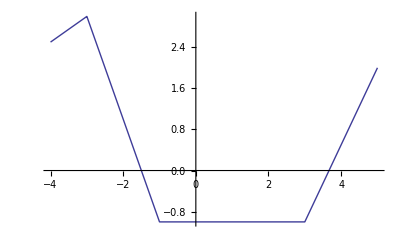

```mathematica
xs={-5,-3,-1,3,5};as={2,3,-1,-1};bs={1/2,-2,0,3/2};
Plot[LinSpline[xs,as,bs,x],{x,-4,5}]
```

```mathematica
f[x1_]:=(-Sin[x1]+100*x1)*0.01Cos[x1];
xs1={5,9,9.5,11,12.5,13.7,14.8,15.2,16.2,17.6,18.7,19.3,20};ys1=Map[f,xs1];
```

```mathematica
{as,bs}=LinSplineCoefs[xs1,ys1];
```

```mathematica
t1=Plot[f[x],{x,5,20},PlotStyle->Red];
```

```mathematica
t2=Plot[LinSpline[xs1,as,bs,x],{x,5,20},PlotStyle->Green];
```

```mathematica
t3=ListPlot[Transpose[{xs1,ys1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[t1,t2,t3]
```

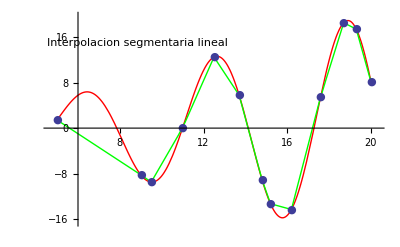

```mathematica
xp0={0,6,19,26,31,35,36};
yp0={13,8,-2,-4.2,-3.3,-1,0};
{as0,bs0}=LinSplineCoefs[xp0,yp0];
```

```mathematica
g0=Plot[LinSpline[xp0,as0,bs0,x],{x,0,36},PlotRange->{-10,22},PlotStyle->Red];
r0=ListPlot[Transpose[{xp0,yp0}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp1={0,6,13,19,21,25,27.2,33.2,36};
yp1={0,8,13,15,15,14,13,7,0};
{as1,bs1}=LinSplineCoefs[xp1,yp1];
```

```mathematica
g1=Plot[LinSpline[xp1,as1,bs1,x],{x,0,36},PlotStyle->Red];
r1=ListPlot[Transpose[{xp1,yp1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp2={19,20,21.5,24,25};
yp2={15,17,20,16,14};
{as2,bs2}=LinSplineCoefs[xp2,yp2];
```

```mathematica
g2=Plot[LinSpline[xp2,as2,bs2,x],{x,19,25},PlotStyle->Orange];
r2=ListPlot[Transpose[{xp2,yp2}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp3={21,22.2,24.9,25.9,27};
yp3={5,7.2,9.9,7,5};
{as3,bs3}=LinSplineCoefs[xp3,yp3];
```

```mathematica
g3=Plot[LinSpline[xp3,as3,bs3,x],{x,21,27},PlotStyle->Brown];
r3=ListPlot[Transpose[{xp3,yp3}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp4={31,31.3,32.1,35};
yp4={-3.3,-1.4,-0.3,-1};
{as4,bs4}=LinSplineCoefs[xp4,yp4];
```

```mathematica
g4=Plot[LinSpline[xp4,as4,bs4,x],{x,31,35},PlotStyle->Black];
r4=ListPlot[Transpose[{xp4,yp4}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp5={0,1,1.2};
yp5={0,4.5,6};
{as5,bs5}=LinSplineCoefs[xp5,yp5];
```

```mathematica
g5=Plot[LinSpline[xp5,as5,bs5,x],{x,0,1.2},PlotStyle->Red];
r5=ListPlot[Transpose[{xp5,yp5}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xp6={0,0.2,1.2};
yp6={13,9,6};
{as6,bs6}=LinSplineCoefs[xp6,yp6];
```

```mathematica
g6=Plot[LinSpline[xp6,as6,bs6,x],{x,0,1.2},PlotStyle->Red];
r6=ListPlot[Transpose[{xp6,yp6}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[g0,g1,g2,g3,g4,g5,g6,r0,r1,r2,r3,r4,r5,r6]
```

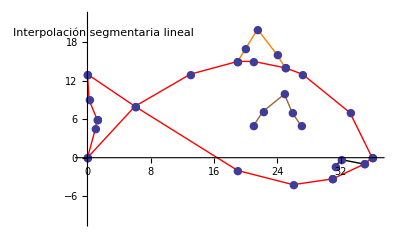

```mathematica
xsv0={8.5,9,10,10.6};
ysv0={3.5,5.3,5.2,4};
{asv0,bsv0}=LinSplineCoefs[xsv0,ysv0];
```

```mathematica
h0=Plot[LinSpline[xsv0,asv0,bsv0,x],{x,8.5,10.6},PlotStyle->Red];
k0=ListPlot[Transpose[{xsv0,ysv0}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv1={8.5,9,10.1,12.3,13.6};
ysv1={3.5,2,1.1,2,4.2};
{asv1,bsv1}=LinSplineCoefs[xsv1,ysv1];
```

```mathematica
h1=Plot[LinSpline[xsv1,asv1,bsv1,x],{x,8.5,13.6},PlotStyle->Red];
k1=ListPlot[Transpose[{xsv1,ysv1}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv2={13,13.6};
ysv2={12,4.2};
{asv2,bsv2}=LinSplineCoefs[xsv2,ysv2];
```

```mathematica
h2=Plot[LinSpline[xsv2,asv2,bsv2,x],{x,13,13.6},PlotStyle->Red];
k2=ListPlot[Transpose[{xsv2,ysv2}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv3={13,13.1,13.2};
ysv3={12,14.5,17};
{asv3,bsv3}=LinSplineCoefs[xsv3,ysv3];
```

```mathematica
h3=Plot[LinSpline[xsv3,asv3,bsv3,x],{x,13,13.2},PlotStyle->Red];
k3=ListPlot[Transpose[{xsv3,ysv3}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv4={9.4,10,12,13.2};
ysv4={12.3,14,16,17};
{asv4,bsv4}=LinSplineCoefs[xsv4,ysv4];
```

```mathematica
h4=Plot[LinSpline[xsv4,asv4,bsv4,x],{x,9.4,13.2},PlotStyle->Red];
k4=ListPlot[Transpose[{xsv4,ysv4}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
xsv5={9.4,10,12,14.5,15.4};
ysv5={12.3,10,9,10,12};
{asv5,bsv5}=LinSplineCoefs[xsv5,ysv5];
```

```mathematica
h5=Plot[LinSpline[xsv5,asv5,bsv5,x],{x,9.4,15.4},PlotStyle->Red];
k5=ListPlot[Transpose[{xsv5,ysv5}],PlotMarkers->{Automatic,Medium}];
```

```mathematica
Show[h0,h1,h2,h3,h4,h5,k0,k1,k2,k3,k4,k5,PlotRange->All]
```